# AssemblyCA Pathways

Keith Y. Patarroyo

University of Glasgow

## Basic

```mathematica
stripMetadata[expression_] := If[Head[expression] === Rule, Last[expression], expression];
```

## 1.2.1 Definition

## One Dimension

```mathematica
atom0 =  "a" ;
atom1 =  "b" ;
step1 =   "bb" ;
step2 =   "abb" ;
step3 =   "aabb" ;
step4 =   "aabbbb" ;
step5 =   "aabbbbbb" ;
step6 =   "aabbbbbbabb" ;

atom0 = Flatten@ToExpression@StringSplit[atom0,""];
atom1 = Flatten@ToExpression@StringSplit[atom1,""];
step1 = Flatten@ToExpression@StringSplit[step1,""];
step2 = Flatten@ToExpression@StringSplit[step2,""];
step3 = Flatten@ToExpression@StringSplit[step3,""];
step4 = Flatten@ToExpression@StringSplit[step4,""];
step5 = Flatten@ToExpression@StringSplit[step5,""];
step6 = Flatten@ToExpression@StringSplit[step6,""];

v={atom0,atom1,step1,step2,step3,step4,step5,step6};e = { Labeled[atom1 -> step1,atom1],Labeled[atom1 -> step1,atom1],Labeled[atom0 -> step2,step1],Labeled[step1 -> step2,atom0],Labeled[atom0 -> step3,step2],Labeled[step2 -> step3,atom0],Labeled[step3 -> step4,step1],Labeled[step1 -> step4,step3],Labeled[step4 -> step5,step1],Labeled[step1 -> step5,step4],Labeled[step5 -> step6,step2],Labeled[step2 -> step6,step5] };
enolabeled = Table[e[[i]][[1]],{i, Length[e]}];
elabeled = Table[Labeled[e[[i]][[1]], Placed[Text[ Framed[Style[stripMetadata[e[[i]][[2]]], Hue[0.62, 1, 0.48], FontSize -> 8], Background -> Directive[Opacity[0.2], Hue[0.1, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]]], 1/2]], {i, Length[e]}];
gim = Graph[v, enolabeled, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {3.5}}];
atoms = {atom0,atom1};
LayeredGraphPlot[gim, atoms -> Left, AspectRatio -> 0.2]
```

-Graphics-

```mathematica
ArrayPlot[{First@#},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}
]&/@{{{a,a,b,b,b,b,b,b,a,b,b},a}}
```

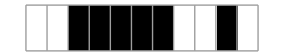

```mathematica
atom0 =  "a" ;
atom1 =  "b" ;
step1 =   "ba" ;
step2 =   "aa" ;
step3 =   "bb" ;
step4 =   "bbb" ;
step5 =   "bbbbb" ;
step6 =   "aabbbbb" ;
step8 =   "babb" ;
step10 =   "aabbbbbaa" ;
step11 =   "aabbbbbaaba" ;
step12 =   "aabbbbbbabb" ;
atom0 = Flatten@ToExpression@StringSplit[atom0,""];
atom1 = Flatten@ToExpression@StringSplit[atom1,""];
step1 = Flatten@ToExpression@StringSplit[step1,""];
step2 = Flatten@ToExpression@StringSplit[step2,""];
step3 = Flatten@ToExpression@StringSplit[step3,""];
step4 = Flatten@ToExpression@StringSplit[step4,""];
step5 = Flatten@ToExpression@StringSplit[step5,""];
step6 = Flatten@ToExpression@StringSplit[step6,""];
step8 = Flatten@ToExpression@StringSplit[step8,""];
step10 = Flatten@ToExpression@StringSplit[step10,""];
step11 = Flatten@ToExpression@StringSplit[step11,""];
step12 = Flatten@ToExpression@StringSplit[step12,""];
v={atom0,atom1,step1,step2,step3,step4,step5,step6,step8,step10,step11,step12};
e = { Labeled[atom1 -> step1,atom0],Labeled[atom0 -> step1,atom1],Labeled[atom0 -> step2,atom0],Labeled[atom0 -> step2,atom0],Labeled[atom1 -> step3,atom1],Labeled[atom1 -> step3,atom1],Labeled[atom1 -> step4,step3],Labeled[step3 -> step4,atom1],Labeled[step4 -> step5,step3],Labeled[step3 -> step5,step4],Labeled[step5 -> step6,step2],Labeled[step2 -> step6,step5],Labeled[step3 -> step8,step1],Labeled[step1 -> step8,step3],Labeled[step6-> step10,step2],Labeled[step2 -> step10,step6],Labeled[step10 -> step11,step1],Labeled[step1 -> step11,step10],Labeled[step8 -> step12,step6],Labeled[step6 -> step12,step8] };
enolabeled = Table[e[[i]][[1]],{i, Length[e]}];
gim = Graph[v, enolabeled, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {2.5}}];
atoms = {atom0,atom1};
LayeredGraphPlot[gim, atoms -> Left, AspectRatio -> 0.4]
```

```mathematica
{{"[◼]", "CommaRow"}}[ArrayPlot[{First@#},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}
]&/@{{step11,a},{step12,a}}]
```

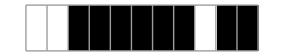
```mathematica
-Graphics-,-Graphics-
```

```mathematica
atom0="a";
atom1="b";
atom2="c";
atom3="d";
step1="bb";
step2="aa";
step3="ba";
step4="bbb";
step5="aabb";
step6="aabbbbb";
step7=step1;
step8="babb";
step9=step6;
step10="aabbbbbaa";
step11="aabbbbbaaba";
step13=step3;
step14="babbb";
step15="babbbba";
step16="babbbbaaa";
step17="babbbbaaaaa";
step18="aabbbbbbabb";
atom0 = Flatten@ToExpression@StringSplit[atom0,""];
atom1 = Flatten@ToExpression@StringSplit[atom1,""];
step1 = Flatten@ToExpression@StringSplit[step1,""];
step2 = Flatten@ToExpression@StringSplit[step2,""];
step3 = Flatten@ToExpression@StringSplit[step3,""];
step4 = Flatten@ToExpression@StringSplit[step4,""];
step5 = Flatten@ToExpression@StringSplit[step5,""];
step6 = Flatten@ToExpression@StringSplit[step6,""];
step7 = Flatten@ToExpression@StringSplit[step7,""];
step8 = Flatten@ToExpression@StringSplit[step8,""];
step9 = Flatten@ToExpression@StringSplit[step9,""];
step10 = Flatten@ToExpression@StringSplit[step10,""];
step11 = Flatten@ToExpression@StringSplit[step11,""];
step13 = Flatten@ToExpression@StringSplit[step13,""];
step14 = Flatten@ToExpression@StringSplit[step14,""];
step15 = Flatten@ToExpression@StringSplit[step15,""];
step16 = Flatten@ToExpression@StringSplit[step16,""];
step17 = Flatten@ToExpression@StringSplit[step17,""];
step18 = Flatten@ToExpression@StringSplit[step18,""];
v={atom0,atom1,step1,step2,step3,step4,step5,step6,step7,step8,step9,step10,step11,step13,step14,step15,step16,step17,step18};
e={Labeled[atom1->step1,atom1],Labeled[atom1->step1,atom1],Labeled[atom0->step2,atom0],Labeled[atom0->step2,atom0],Labeled[atom1->step3,atom0],Labeled[atom0->step3,atom1],Labeled[atom1->step4,step1],Labeled[step1->step4,atom1],Labeled[step1->step5,step2],Labeled[step2->step5,step1],Labeled[step5->step6,step4],Labeled[step4->step6,step5],Labeled[step7->step8,step3],Labeled[step3->step8,step7],Labeled[step9->step10,step2],Labeled[step2->step10,step9],Labeled[step10->step11,step3],Labeled[step3->step11,step10],Labeled[step13->step14,step4],Labeled[step4->step14,step13],Labeled[step14->step15,step3],Labeled[step3->step15,step14],Labeled[step15->step16,step2],Labeled[step2->step16,step15],Labeled[step16->step17,step2],Labeled[step2->step17,step16],Labeled[step8->step18,step6],Labeled[step6->step18,step8]};
enolabeled=Table[e[[i]][[1]],{i,Length[e]}];
gim = Graph[v, enolabeled, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {3.5}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
{{"[◼]", "CommaRow"}}[ArrayPlot[{First@#},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}
]&/@{{step11,a},{step18,a},{step17,a}}]
```

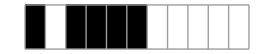
```mathematica
-Graphics-,-Graphics-,-Graphics-
```

## Two Dimensions

```mathematica
a1 = ArrayPlot[{{1,0},{1,1}},Mesh->All, ColorRules -> {1 -> White, 0 -> Black},ImageSize->{100,Automatic}];
a2 = ArrayPlot[{{1,1},{0,1}},Mesh->All, ColorRules -> {1 -> White, 0 -> Black},ImageSize->{100,Automatic}];
a4 = ArrayPlot[{{0,1},{1,1}},Mesh->All, ColorRules -> {1 -> White, 0 -> Black},ImageSize->{100,Automatic}];
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step5 = ArrayPlot[{{a,b,a,a},{a,a,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step6 = GraphicsGrid[{{a1,a2},{"",a4}},Spacings->{-13,-13},ImageSize->Tiny];
step7 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
v={atom0,atom1,step1,step2,step3,step4,step5,step6,step7};
e = {atom0->step1,atom0->step1,atom1->step2,atom0->step2,step2->step3,step2->step3,step2->step4,step1->step3,step4->step5,step4->step5,step5->step6,step4->step6,step6->step7,step3->step7};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.2]
```

-Graphics-

```mathematica
step7
```

-Graphics-

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3 = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4 = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step6b},{step8b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e = {atom0->step1,atom0->step1,atom1->step3,atom1->step3,atom1->step2,atom0->step2,atom1->step4,atom0->step4,step1->step5,step4->step5,step1->step6,step2->step6,step1->step7,step2->step7,step1->step8,step3->step8,step8->step9,step7->step9,step6->step10,step9->step10,step5->step11,step10->step11};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

-Graphics-

```mathematica
step7
```

-Graphics-

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3 = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4 = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step9 = ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9b = ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = ArrayPlot[{{a,a},{b,a},{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11 = GraphicsGrid[{{"",step6b},{step9b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step12 = GraphicsGrid[{{"",step6b},{step8b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step13 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step14 = ArrayPlot[{{a,a,a,a},{b,a,b,a},{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e = {atom0->step1,atom0->step1,atom1->step3,atom1->step3,atom1->step2,atom0->step2,atom1->step4,atom0->step4,step1->step5,step4->step5,step1->step6,step2->step6,step1->step7,step2->step7,step1->step8,step3->step8,step4->step9,step4->step9,step6->step10,step7->step10,step9->step11,step10->step11,step8->step12,step10->step12,step5->step13,step12->step13,step6->step14,step11->step14};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

-Graphics-

```mathematica
{step13,step14}
```

{-Graphics-,-Graphics-}

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step1b = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2b = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step3 = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3b = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step4 = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4b = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step5 = ArrayPlot[{{a,b, a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step6 = ArrayPlot[{{b,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
a5= ArrayPlot[{{1,1}}, ColorRules -> {1 -> White, 0 -> Black},Frame->False,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step2b},{step2b,step2b},{step4b,""}},Spacings->{-13,-2},ImageSize->Tiny];
step11 = GraphicsGrid[{{"",step2b},{"",step2b},{step1b,step1b}},Spacings->{-13,-13},ImageSize->Tiny];
step12 = GraphicsGrid[{{step4b,step1b},{"",step2b},{"",step2b},{step1b,step1b}},Spacings->{-13,-2},ImageSize->Tiny];
step13 = GraphicsGrid[{{step1b,step1b},{"",step2b},{step2b,step2b},{step4b,""}},Spacings->{-13,-2},ImageSize->Tiny];
step14 = ArrayPlot[{{a,a,a,a},{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step15 = ArrayPlot[{{a,a,a,a},{b,a,b,a},{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step16 = GraphicsGrid[{{step1b,step1b},{step1b,step2b},{step2b,step2b},{step4b,""}},Spacings->{-13,-2},ImageSize->Tiny];
step17 = GraphicsGrid[{{step4b,step1b},{step1b,step2b},{"",step2b},{step1b,step1b}},Spacings->{-13,-2},ImageSize->Tiny];
step18 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step19 = ArrayPlot[{{a,a,a,a},{a,a,b,a},{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e = {atom0->step1,atom0->step1,atom1->step3,atom1->step3,atom1->step2,atom0->step2,atom1->step4,atom0->step4,step1->step5,step4->step5,step2->step6,step4->step6,step2->step7,step2->step7,step1->step8,step1->step8,step7->step9,step6->step9,step7->step10,step6->step10,step8->step11,step7->step11,step5->step12,step11->step12,step8->step13,step10->step13,step9->step14,step8->step14,step14->step15,step5->step15,step1->step16,step13->step16,step1->step17,step12->step17,step2->step19,step16->step19,step3->step18,step17->step18};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
{step15,step18,step19}
```

{-Graphics-,-Graphics-,-Graphics-}

## Extra Blocks

```mathematica
ArrayPlot[{{b,b,a,a},{b,a,a,a},{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{b,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{a,b,a},{b,a,b},{a,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{a,b,b},{b,a,b},{a,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{a,b,b},{b,a,b},{b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

```mathematica
ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}]
```

-Graphics-

## 1.2.2 Hash Assembly

## One Dimension

```mathematica
atom0="a";
atom1="b";
step1="bb";
step2a="abb";
step3a="aabb";
step4a="aabbbb";
step5a="aabbbbbb";
step6a="aabbbbbbabb";
step2="aa";
step3b="aab";
step4b="aaba";
step5b="bbaaba";
step6b="bbbbaaba";
step7b="aabbbbbaaba";
step3="ba";
step4c="bbb";
step5c="bbbba";
step6c="babbbba";
step7c="babbbbaaa";
step8c="babbbbaaaaa";
atom0=Flatten@ToExpression@StringSplit[atom0,""];
atom1=Flatten@ToExpression@StringSplit[atom1,""];
step1=Flatten@ToExpression@StringSplit[step1,""];
step2a=Flatten@ToExpression@StringSplit[step2a,""];
step3a=Flatten@ToExpression@StringSplit[step3a,""];
step4a=Flatten@ToExpression@StringSplit[step4a,""];
step5a=Flatten@ToExpression@StringSplit[step5a,""];
step6a=Flatten@ToExpression@StringSplit[step6a,""];
step2=Flatten@ToExpression@StringSplit[step2,""];
step3b=Flatten@ToExpression@StringSplit[step3b,""];
step4b=Flatten@ToExpression@StringSplit[step4b,""];
step5b=Flatten@ToExpression@StringSplit[step5b,""];
step6b=Flatten@ToExpression@StringSplit[step6b,""];
step7b=Flatten@ToExpression@StringSplit[step7b,""];
step3=Flatten@ToExpression@StringSplit[step3,""];
step4c=Flatten@ToExpression@StringSplit[step4c,""];
step5c=Flatten@ToExpression@StringSplit[step5c,""];
step6c=Flatten@ToExpression@StringSplit[step6c,""];
step7c=Flatten@ToExpression@StringSplit[step7c,""];
step8c=Flatten@ToExpression@StringSplit[step8c,""];
v={atom0,atom1,step1,step2,step3,step4c,step5c,step6c,step7c,step8c,step3b,step4b,step5b,step6b,step7b,step2a,step3a,step4a,step5a,step6a};
e={Labeled[atom1->step1,atom1],Labeled[atom1->step1,atom1],Labeled[atom0->step2a,step1],Labeled[step1->step2a,atom0],Labeled[atom0->step3a,step2a],Labeled[step2a->step3a,atom0],Labeled[step3a->step4a,step1],Labeled[step1->step4a,step3a],Labeled[step4a->step5a,step1],Labeled[step1->step5a,step4a],Labeled[step5a->step6a,step2a],Labeled[step2a->step6a,step5a],Labeled[atom0->step2,atom0],Labeled[atom0->step2,atom0],Labeled[step2->step3b,atom1],Labeled[atom1->step3b,step2],Labeled[atom0->step4b,step3b],Labeled[step3b->step4b,atom0],Labeled[step4b->step5b,step1],Labeled[step1->step5b,step4b],Labeled[step5b->step6b,step1],Labeled[step1->step6b,step5b],Labeled[step6b->step7b,step3b],Labeled[step3b->step7b,step6b],Labeled[atom0->step3,atom1],Labeled[atom1->step3,atom0],Labeled[step1->step4c,atom0],Labeled[atom0->step4c,step1],Labeled[step4c->step5c,step3],Labeled[step3->step5c,step4c],Labeled[step5c->step6c,step3],Labeled[step3->step6c,step5c],Labeled[step6c->step7c,step2],Labeled[step2->step7c,step6c],Labeled[step7c->step8c,step2],Labeled[step2->step8c,step7c]};
enolabeled = Table[e[[i]][[1]],{i, Length[e]}];
enolabeled = Table[e[[i]][[1]],{i, Length[e]}];
gim = Graph[v, enolabeled, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {6.5}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
atom0 =  "a" ;
atom0a =  "a" ;
atom1 =  "b" ;
atom1a =  "b" ;
atom1b =  "b" ;
atom1c =  "b" ;
atom1d =  "b" ;
atom1e =  "b" ;
step1 = "aa";
step2="bb";
step2a="bb";
step2b="bb";
step3="ab";
step4="aabb";
step5a="bbbb";
step6a="aabbbbbb";
step7a="aabbbbbbab";
step8a="aabbbbbbabb";
atsa = {atom0 ,atom0a };
atsb = {atom1 ,atom1a ,atom1b ,atom1c ,atom1d ,atom1e};
stepsb = {step2,step2a,step2b};
rest = {step1,step4,step5a,step6a};
sizes = {50,100,100,200};
rest1 = {atom0,atom1,step3};
sizesRest1 = {25,25,50};
atsaArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atsa[[i]],""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, Length[atsa]}];
atsbArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atsb[[i]],""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, Length[atsb]}];
stepsbArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[stepsb[[i]],""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}],i],{i, Length[stepsb]}];
restArray = Table[ArrayPlot[{Flatten@ToExpression@StringSplit[rest[[i]],""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{sizes[[i]],Automatic}],{i, Length[rest]}];
rest1Array = Table[ArrayPlot[{Flatten@ToExpression@StringSplit[rest1[[i]],""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{sizesRest1[[i]],Automatic}],{i, Length[rest1]}];
e={restArray[[1]]->atsaArray[[1]],restArray[[1]]->atsaArray[[2]],stepsbArray[[1]]->atsbArray[[1]],stepsbArray[[1]]->atsbArray[[2]],stepsbArray[[2]]->atsbArray[[3]],stepsbArray[[2]]->atsbArray[[4]],stepsbArray[[3]]->atsbArray[[5]],stepsbArray[[3]]->atsbArray[[6]],restArray[[2]]->restArray[[1]],restArray[[2]]->stepsbArray[[1]],restArray[[3]]->stepsbArray[[2]],restArray[[3]]->stepsbArray[[3]],restArray[[4]]->restArray[[3]],restArray[[4]]->restArray[[2]]};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={restArray[[4]]};
LayeredGraphPlot[gim,atoms->Top,AspectRatio->0.6]
```

-Graphics-

```mathematica
gim=Graph[{rest1Array[[3]]->rest1Array[[1]],rest1Array[[3]]->rest1Array[[2]]},{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={rest1Array[[3]]};
LayeredGraphPlot[gim,atoms->Top,AspectRatio->1.4]
```

-Graphics-

```mathematica
atom0 =  "a" ;
atom0a =  "a" ;
atom1 =  "b" ;
atom1a =  "b" ;
atom1b =  "b" ;
atom1c =  "b" ;
atom1d =  "b" ;
atom1e =  "b" ;
step1 = "aa";
step2="bb";
step2a="bb";
step2b="bb";
step3="ab";
step4="aabb";
step5a="bbbb";
step6a="aabbbbbb";
step7a="aabbbbbbab";
step8a="aabbbbbbabb";
atom0 =  Flatten@ToExpression@StringSplit[atom0,""];
atom1 =  Flatten@ToExpression@StringSplit[atom1,""];
step1 = Flatten@ToExpression@StringSplit[step1,""];
step2=Flatten@ToExpression@StringSplit[step2,""];
step3=Flatten@ToExpression@StringSplit[step3,""];
step4=Flatten@ToExpression@StringSplit[step4,""];
step5a=Flatten@ToExpression@StringSplit[step5a,""];
step6a=Flatten@ToExpression@StringSplit[step6a,""];
step7a=Flatten@ToExpression@StringSplit[step7a,""];
step8a=Flatten@ToExpression@StringSplit[step8a,""];
v={atom0,atom1,step1,step2,step3,step4,step5a,step6a,step7a,step8a};
e={atom0->step1,atom0->step1,atom1->step2,atom1->step2,atom1->step3,atom0->step3,step1->step4,step2->step4,step2->step5a,step2->step5a,step5a->step6a,step4->step6a,step6a->step7a,step3->step7a,step7a->step8a,atom1->step8a};
gim = Graph[v, e, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {6.5}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Bottom,AspectRatio->1.5]
```

-Graphics-

```mathematica
{-Graphics-,restArray[[4]],rest1Array[[3]],rest1Array[[2]]}
```

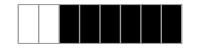
```mathematica
{-Graphics-,-Graphics- ,-Graphics-,-Graphics-}
```

```mathematica
atom0 =  "a" ;
atom1 =  "b" ;
step1 = "aa";
step2="bb";
step3="ab";
step4="aabb";
step5a="bbbb";
step6a="aabbbbbb";
step7a="aabbbbbbab";
step8a="aabbbbbbabb";
step5="ba";
step6b="bbba";
step7b="aabbbbba";
step8b="aabbbbbaab";
step9b="aabbbbbaaba";
step4c="babb";
step5c="bbaa";
step6c="babbbbaa";
step7c="babbbbaaaa";
step8c="babbbbaaaaa";
atom0 =  Flatten@ToExpression@StringSplit[atom0,""];
atom1 =  Flatten@ToExpression@StringSplit[atom1,""];
step1 = Flatten@ToExpression@StringSplit[step1,""];
step2=Flatten@ToExpression@StringSplit[step2,""];
step3=Flatten@ToExpression@StringSplit[step3,""];
step4=Flatten@ToExpression@StringSplit[step4,""];
step5a=Flatten@ToExpression@StringSplit[step5a,""];
step6a=Flatten@ToExpression@StringSplit[step6a,""];
step7a=Flatten@ToExpression@StringSplit[step7a,""];
step8a=Flatten@ToExpression@StringSplit[step8a,""];
step5=Flatten@ToExpression@StringSplit[step5,""];
step6b=Flatten@ToExpression@StringSplit[step6b,""];
step7b=Flatten@ToExpression@StringSplit[step7b,""];
step8b=Flatten@ToExpression@StringSplit[step8b,""];
step9b=Flatten@ToExpression@StringSplit[step9b,""];
step4c=Flatten@ToExpression@StringSplit[step4c,""];
step5c=Flatten@ToExpression@StringSplit[step5c,""];
step6c=Flatten@ToExpression@StringSplit[step6c,""];
step7c=Flatten@ToExpression@StringSplit[step7c,""];
step8c=Flatten@ToExpression@StringSplit[step8c,""];
v={atom0,atom1,step1,step2,step3,step4,step5,step4c,step5c,step6c,step7c,step8c,step6b,step7b,step8b,step9b,step5a,step6a,step7a,step8a};
e={atom0->step1,atom0->step1,atom1->step2,atom1->step2,atom1->step3,atom0->step3,atom1->step5,atom0->step5,step1->step4,step2->step4,step2->step5a,step2->step5a,step5a->step6a,step4->step6a,step6a->step7a,step3->step7a,step7a->step8a,atom1->step8a,step2->step6b,step5->step6b,step4->step7b,step6b->step7b,step7b->step8b,step3->step8b,step8b->step9b,atom0->step9b,step5->step4c,step2->step4c,step2->step5c,step1->step5c,step4c->step6c,step5c->step6c,step1->step7c,step6c->step7c,step7c->step8c,atom0->step8c};
gim = Graph[v, e, {AspectRatio -> 1, EdgeStyle -> {Directive[{Hue[0.62, 0.85, 0.87], Dashing[None], AbsoluteThickness[1]}]}, FormatType -> TraditionalForm, GraphLayout -> {"Dimension" -> 2}, PerformanceGoal -> "Quality", VertexShapeFunction -> {Inset[ArrayPlot[{#2}, ColorRules -> {a-> White, b -> Black}, Mesh -> True,ImageSize->{Scaled[10],Scaled[10]},AspectRatio->Automatic], #1, Center, First[#3]] & },VertexSize -> {6.5}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

## Two Dimensions

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3 = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4 = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9b = ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step9c= ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10b = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11b = ArrayPlot[{{b,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12b = ArrayPlot[{{b,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11c = ArrayPlot[{{b,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step12c = ArrayPlot[{{b,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step13b = ArrayPlot[{{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step14b = ArrayPlot[{{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step6b},{step8b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step15b = GraphicsGrid[{{"",step6b},{step9c,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step16b = GraphicsGrid[{{"",step6b},{step11c,step12c}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step12 = ArrayPlot[{{a,a,a,a},{b,a,b,a},{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step13 = ArrayPlot[{{a,a,a,a},{a,a,b,a},{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e = {atom0->step1,atom0->step1,atom1->step3,atom1->step3,atom1->step2,atom0->step2,atom1->step4,atom0->step4,step1->step5,step4->step5,step1->step6,step2->step6,step1->step7,step2->step7,step1->step8,step3->step8,step8->step9,step7->step9,step6->step10,step9->step10,step5->step11,step10->step11,step7->step13b,step9b->step13b,step6->step15b,step13b->step15b,step6->step12,step15b->step12,step1->step10b,step1->step10b,step4->step9b,step4->step9b,step11b->step14b,step12b->step14b,step14b->step16b,step6->step16b,step10b->step13,step16b->step13,step2->step11b,step4->step11b,step2->step12b,step2->step12b};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
atom0 =  "a" ;
atom1 =  "b" ;
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
atsaArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atom0,""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, 11}];
atsbArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atom1,""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, 5}];
e={step8->atsaArray[[1]],step8->atsaArray[[2]],step8->atsbArray[[1]],step8->atsbArray[[2]],step7->atsaArray[[3]],step7->atsaArray[[4]],step7->atsaArray[[5]],step7->atsbArray[[3]],step6->atsbArray[[4]],step6->atsaArray[[6]],step6->atsaArray[[7]],step6->atsaArray[[8]],step5->atsaArray[[9]],step5->atsaArray[[10]],step5->atsbArray[[5]],step5->atsaArray[[11]],step11->step8,step11->step7,step11->step6,step11->step5};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={step11};
LayeredGraphPlot[gim,atoms->Top,AspectRatio->0.6]
```

-Graphics-

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom0a = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
atom1a = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12tri = GraphicsGrid[{{"",atom1a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step13tri = GraphicsGrid[{{"",atom0a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step14tri = GraphicsGrid[{{"",atom0a},{atom1a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step6b},{step8b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e={atom0->step1,atom0->step1,atom1->step2,atom0->step2,step8->step9,step7->step9,step6->step10,step9->step10,step5->step11,step10->step11,step1->step12tri,atom1->step12tri,step1->step13tri,atom0->step13tri,step2->step14tri,atom0->step14tri,atom0->step5,step12tri->step5,atom1->step8,step12tri->step8,atom1->step7,step13tri->step7,atom0->step6,step14tri->step6};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Bottom,AspectRatio->1.2]
```

```mathematica
{-Graphics-}
```

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step3 = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step4 = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12tri = GraphicsGrid[{{"",atom1a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step13tri = GraphicsGrid[{{"",atom0a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step14tri = GraphicsGrid[{{"",atom0a},{atom1a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step15tri = GraphicsGrid[{{"",atom1a},{atom0a,atom1a}},Spacings->{-13,-13},ImageSize->{50,50}];
step16tri = GraphicsGrid[{{"",atom0a},{atom0a,atom1a}},Spacings->{-13,-13},ImageSize->{50,50}];
step5 = ArrayPlot[{{a,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{b,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9b = ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step9c= ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10b = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11b = ArrayPlot[{{b,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12b = ArrayPlot[{{b,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step11c = ArrayPlot[{{b,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step12c = ArrayPlot[{{b,a},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step13b = ArrayPlot[{{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step14b = ArrayPlot[{{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step6b},{step8b,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step15b = GraphicsGrid[{{"",step6b},{step9c,step7b}},Spacings->{-13,-13},ImageSize->Tiny];
step16b = GraphicsGrid[{{"",step6b},{step11c,step12c}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{a,b,a,a},{a,a,b,a},{b,b,b,a},{a,a,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step12 = ArrayPlot[{{a,a,a,a},{b,a,b,a},{a,b,b,a},{a,b,a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step13 = ArrayPlot[{{a,a,a,a},{a,a,b,a},{b,a,b,a},{a,b,b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e = {atom0->step1,atom0->step1,atom1->step2,atom0->step2,atom1->step4,atom0->step4,step8->step9,step7->step9,step6->step10,step9->step10,step5->step11,step10->step11,step7->step13b,step9b->step13b,step6->step15b,step13b->step15b,step6->step12,step15b->step12,step11b->step14b,step12b->step14b,step14b->step16b,step6->step16b,step10b->step13,step16b->step13,step1->step12tri,atom1->step12tri,step1->step13tri,atom0->step13tri,step2->step14tri,atom0->step14tri,atom0->step5,step12tri->step5,atom1->step8,step12tri->step8,atom1->step7,step13tri->step7,atom0->step6,step14tri->step6,atom1->step15tri,step4->step15tri,atom0->step16tri,step4->step16tri,step14tri->step12b,atom1->step12b,step16tri->step11b,atom1->step11b,step13tri->step10b,atom0->step10b,step15tri->step9b,atom0->step9b};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

## Extra Blocks

```mathematica
atom0 =  "a" ;
atom1 =  "b" ;
step5 = ArrayPlot[{{b,b},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = Subscript[ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}],2];
step7 = ArrayPlot[{{a,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = Subscript[ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}],1];
step11 = ArrayPlot[{{b,b,a,a},{b,a,a,a},{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
atsaArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atom0,""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, 10}];
atsbArray = Table[Subscript[ArrayPlot[{Flatten@ToExpression@StringSplit[atom1,""]},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}],i],{i, 6}];
e={step8->atsaArray[[1]],step8->atsaArray[[2]],step8->atsaArray[[3]],step8->atsaArray[[4]],step7->atsbArray[[1]],step7->atsbArray[[2]],step7->atsbArray[[3]],step7->atsaArray[[5]],step6->atsaArray[[6]],step6->atsaArray[[7]],step6->atsaArray[[8]],step6->atsaArray[[9]],step5->atsbArray[[4]],step5->atsaArray[[10]],step5->atsbArray[[5]],step5->atsbArray[[6]],step11->step8,step11->step7,step11->step6,step11->step5};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={step11};
LayeredGraphPlot[gim,atoms->Top,AspectRatio->0.6]
```

-Graphics-

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom0a = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
atom1a = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
stepx = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12tri = GraphicsGrid[{{"",atom1a},{atom1a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step13tri = GraphicsGrid[{{"",atom0a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step14tri = GraphicsGrid[{{"",atom1a},{atom1a,atom1a}},Spacings->{-13,-13},ImageSize->{50,50}];
step5 = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step7b},{step7b,step6b}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{b,b,a,a},{b,a,a,a},{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e={atom0->step1,atom0->step1,atom1->step2,atom0->step2,atom1->stepx,atom1->stepx,step7->step9,step6->step9,step7->step10,step9->step10,step8->step11,step10->step11,step2->step12tri,atom1->step12tri,step1->step13tri,atom0->step13tri,stepx->step14tri,atom1->step14tri,step12tri->step5,atom1->step8,step12tri->step8,atom0->step7,step13tri->step7,atom0->step6,step14tri->step6};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Bottom,AspectRatio->1.4]
```

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom0a = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
atom1a = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
stepx = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step12tri = GraphicsGrid[{{"",atom1a},{atom1a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step13tri = GraphicsGrid[{{"",atom0a},{atom0a,atom0a}},Spacings->{-13,-13},ImageSize->{50,50}];
step14tri = GraphicsGrid[{{"",atom1a},{atom1a,atom1a}},Spacings->{-13,-13},ImageSize->{50,50}];
step5 = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6 = ArrayPlot[{{a,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step7 = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8 = ArrayPlot[{{b,b},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step8x = ArrayPlot[{{b,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step6b = ArrayPlot[{{a,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step7b = ArrayPlot[{{a,a},{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8b = ArrayPlot[{{b,b},{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step8xb = ArrayPlot[{{b,b},{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9 = ArrayPlot[{{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step9x = ArrayPlot[{{a,a,b,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step10 = GraphicsGrid[{{"",step7b},{step7b,step6b}},Spacings->{-13,-13},ImageSize->Tiny];
step10x = GraphicsGrid[{{"",step7b},{step7b,step8xb}},Spacings->{-13,-13},ImageSize->Tiny];
step11 = ArrayPlot[{{b,b,a,a},{b,a,a,a},{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step11x = ArrayPlot[{{b,b,a,a},{b,b,a,a},{a,a,b,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e={atom0->step1,atom0->step1,atom1->step2,atom0->step2,atom1->stepx,atom1->stepx,step7->step9,step6->step9,step7->step10,step9->step10,step8->step11,step10->step11,step2->step12tri,atom1->step12tri,step1->step13tri,atom0->step13tri,stepx->step14tri,atom1->step14tri,step12tri->step5,atom1->step8,step12tri->step8,atom0->step7,step13tri->step7,atom0->step6,step14tri->step6,step14tri->step8x,atom1->step8x,step8x->step9x,step7->step9x,step9x->step10x,step7->step10x,step10x->step11x,step8x->step11x};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```

```mathematica
atom0 = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom1 = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{25,Automatic}];
atom0a = ArrayPlot[{{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
atom1a = ArrayPlot[{{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{200,Automatic}];
step1 = ArrayPlot[{{a,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step2 = ArrayPlot[{{b,a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
stepx = ArrayPlot[{{b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{50,Automatic}];
step5 = ArrayPlot[{{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step5a = ArrayPlot[{{a},{a},{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{200,Automatic}];
step5b = ArrayPlot[{{a},{a}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{200,Automatic}];
step6b = ArrayPlot[{{b},{b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{200,Automatic}];
step7b = ArrayPlot[{{a,a},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{400,Automatic}];
step8b = ArrayPlot[{{a,b},{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{400,Automatic}];
step2i = ArrayPlot[{{a,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{400,Automatic}];
step12tri = GraphicsGrid[{{"",step5a},{step2i,atom1a}},Spacings->{-113,-223},ImageSize->{100,100}];
step13tri = GraphicsGrid[{{"",step5b},{step7b,step6b}},Spacings->{-103,-23},ImageSize->{100,100}];
step14tri = GraphicsGrid[{{"",step5b},{step8b,step6b}},Spacings->{-103,-23},ImageSize->{100,100}];
step11 = ArrayPlot[{{b,b,a,a},{b,a,a,a},{a,a,a,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
step11x = ArrayPlot[{{b,b,a,a},{b,b,a,a},{a,a,b,b},{a,a,b,b}},
ColorRules->{a->White,b->Black},
Mesh->True,ImageSize->{100,Automatic}];
e={atom0->step1,atom0->step1,atom1->step2,atom0->step2,atom1->stepx,atom1->stepx,step1->step5,stepx->step5,step5->step12tri,step2->step12tri,step1->step13tri,step12tri->step13tri,step2->step14tri,step12tri->step14tri,step13tri->step11,step13tri->step11,step14tri->step11x,step14tri->step11x};
gim=Graph[e,{AspectRatio->1,EdgeStyle->{Directive[{Hue[0.62,0.85,0.87],Dashing[None],AbsoluteThickness[1]}]},FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},PerformanceGoal->"Quality",VertexShapeFunction->{Text[Framed[Style[stripMetadata[#2],Hue[0.62,1,0.48]],Background->Directive[Opacity[0.0],Hue[0.62,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.0],Hue[0.62,0.52,0.82]]],#1,{0,0}]&}}];
atoms={atom0,atom1};
LayeredGraphPlot[gim,atoms->Left,AspectRatio->0.4]
```